## An analytic equation of state for a neutrino

## Option 1: tanh

A tanh can describe the standard neutrino equation of state quite well:

```mathematica
w[a_]:=1/6(1-Tanh[k Log[a/a0]])
```

Where we have already forced that the w(a → 0) = 1/3 and w(a → ∞) = 0. Here a_0 is defined as w(a=a_0)=1/6, and k describes the slope of the change.

Among other things, we’re interested in its derivative:

```mathematica
D[w[a],a]
```

-(k Sech[k Log[a/a0]]^2)/(6 a)

Now, our goal is to compute the evolution of the energy density, given by

ρ(a)=ρ_ini exp{-3(∫_a_ini)^a da/a(1+w(a))} ,                         (1)

where a_ini  is a scale factor in which neutrinos are relativistic for sure (by default this is a_ini=10^-14). 
Then, this integral is easily computed by changing variables to u = log(a):

```mathematica
wlog[u_]:= 1/6(1-Tanh[k (u - Log[a0])]);
intw[a_]:=Integrate[1+wlog[u],u]/. u-> Log[a]
intw[a]
```

(7 Log[a])/6-Log[Cosh[k (Log[a]-Log[a0])]]/(6 k)

Now, in order for our procedure to be compatible with CLASS, this is not enough. With massive neutrinos, CLASS computes ρ by integrating the distribution function:

ρ = 4π a^-4 ∫dq q^2 ϵ f_0(q), with ϵ = √(q^2+a^2 m^2)

The mass in the energy already implements the transition from a^-4 to a^-3, i.e. the equation of state. 
What I want to do is to modify this formula to replicate (1) with an arbitrary equation of state, i.e.

ρ = 4π  η(a)∫dq q^2 q f_0(q),            (2)

where η(a) must be related to the exponential in (1) and fulfill

η(a→0)∝ a^-4,η(a→∞)∝ a^-3.

That is, we want to compute the neutrino energy density as it they were massless, but make them evolve in time arbitrarily, such that they evolve with a^(-3(1+w)) at any given time.

Now, what is η(a)? Naively, one could say that

η(a)=η_naive(a)= exp{-3(∫_a_ini)^a da/a(1+w(a))},

but this is wrong (close to right, though). This is because η_naive(a) is dependent of a_ini, which is an arbitrary choice by definition.
Namely, one can obtain that η_naive(a)∝a_ini^4 (if one notices that a_ini << a_0). This should be a property of all equations of state which tend to w = 1/3.

Therefore, the right choice for η(a) is

η(a) =a_ini^-4 exp{-3(∫_a_ini)^a  da/a(1+w(a))},            (3)

which is independent of a_ini. 

It is easy to see that this is the right choice by checking the computation of ρ_ini from (2):

ρ_ini= 4π  η(a_ini)∫dq q^2 q f_0(q) = 
        4π a_ini^-4 exp{-3(∫_a_ini)^a_ini da/a(1+w(a))}∫dq q^2 q f_0(q)=
      4π a_ini^-4 ∫dq q^2 q f_0(q),

which is what we where looking for.

So, in principle, for our tanh formula what we are looking for is

```mathematica
η[a_]:= aini^-4 Exp[-3(intw[a]-intw[aini])]
```

```mathematica
FullSimplify[η[a],Assumptions->{aini>0,a0>0,k>0,a>0}]
```

(Cosh[k Log[a/a0]] Sech[k Log[aini/a0]])^(1/2/k)/(√(a^7 aini))

However, this does not take profit of a_ini <<a_0. If one uses this (manually), one gets

```mathematica
η[a_]:= Cosh[k Log[a/a0]]^(1/(2k))/a^(7/2) 2^(1/(2k))/(√a0)
```

This formula has the benefit that one can analitically cancel a_ini, and no need for it to be numerically cancelled. This is the formula which has been implemented in my version of class with the name integral_w_nufld_tanh.

### Plots

-(0.151475 Sech[0.90885 Log[95.5 a]]^2)/a

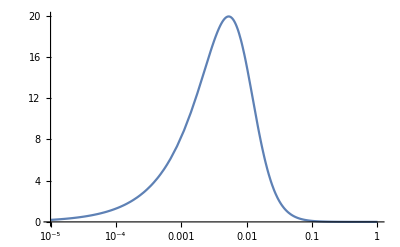

```mathematica
k = 0.90885;
a0 =0.01047120;
D[w[a],a]
LogLinearPlot[-D[w[a],a]/. a-> a1,{a1,10^-5,1},PlotRange->Full]
Clear[k,a0]
```